```mathematica
ResourceFunction["MaTeXInstall"][];
<<MaTeX`;
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->14};
```

# Plots for the WCP-SDQC paper

## Correctness

```mathematica
K[η_,ν_, νp_,N_,δ_ ]:= ((2 - Exp[-η ν]- Exp[-η νp])/2 -δ)N
```

```mathematica
RandomVariate[PoissonDistribution[3]]
```

```mathematica
data=RandomVariate[NormalDistribution[1,3],10^4];
```

```mathematica
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[NormalDistribution[1,3],x],{x,-9,9},PlotStyle->Thick]]
```

```mathematica
data=RandomVariate[PoissonDistribution[3],10^4];
Show[
Histogram[data,20,"ProbabilityDensity"],
DiscretePlot[PDF[PoissonDistribution[3],x],{x,0,14},PlotStyle->Thick, ExtentSize->0.5]
]
```

## DKL vs GLMO plot

```mathematica
b[ν_]:= ν Exp[-ν]
c[ν_]:= ν^2/2 Exp[-ν];
cgeq2[ν_]:=1-Exp[-ν]-ν Exp[-ν];
cgeq3[ν_]:=1-Exp[-ν]-ν Exp[-ν]-ν^2/2 Exp[-ν];
DKL[η_,ν_, N_]:= (1-Exp[-η ν] )N;
GLMO[η_,ν_,νp_, N_]:=N/2(c[νp](1-Exp[-η ν])-c[ν](1-Exp[-η νp]));
```

### Interactive/visualisation

```mathematica
(*DKL only plot*)
Manipulate[Plot[{cgeq2[ν],DKL[η,ν, 1]},{ν,0,10},PlotLegends->{"Upper bound","Threshold"},PlotRange->All],{η,0,1}]
(*GLMO only plot
N = 2 factor to remove it since same on both sides *)
Manipulate[Plot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν]),GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])},{ν,0,2},PlotLegends->{"Upper bound","Threshold"},PlotRange->{0,0.5}, PlotStyle->{Directive[Blue],Directive[Orange]}],{η,0,1},{α,0,1}]
(*Manipulate[Plot[{c[ν]cgeq3[α ν],GLMO[η,α ν,ν, 2]},{ν,0,2},PlotLegends->{"Upper bound","Threshold"},PlotRange->All],{η,0,1},{α,0,1}]*)
Manipulate[Plot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν]),GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν]),cgeq2[ν],DKL[η,ν, 1]},{ν,0,2},PlotLegends->{"GLMO - Upper bound","GLMO - Threshold", "DKL - Upper bound", "DKL - Threshold"},PlotRange->{0,0.5}],{η,0,1},{α,0,1}] (*, PlotStyle->{Directive[Blue],Directive[Orange]}*)
Manipulate[Show[RegionPlot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])<GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])},{ν,0,2},{y,0,0.5},PlotStyle->{LightRed,Opacity[.7]}],RegionPlot[cgeq2[ν]<DKL[η,ν, 1],{ν,0,2},{y,0,0.5},PlotStyle->{LightBlue,Opacity[.7]}],Plot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν]),GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν]),cgeq2[ν],DKL[η,ν, 1]},{ν,0,2},PlotStyle->{Directive[Red, Thick,Dashed],Directive[Red, Thick],Directive[Blue, Thick,Dashed],Directive[Blue, Thick]}, PlotLegends->{"GLMO - Upper bound","GLMO - Threshold", "DKL - Upper bound", "DKL - Threshold"},PlotRange->{0,0.5}],Frame->True,FrameLabel->{"ν"},BaseStyle->texStyle,FrameStyle->Directive[AbsoluteThickness[2],Black],ImageSize->500,FrameTicksStyle->18,LabelStyle->20],{η,0,1},{α,0,1}] 

(*Manipulate[Show[ RegionPlot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])<GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])},{ν,0,2},{y,-2,2},PlotStyle->{LightBlue,Opacity[.7]}],Plot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν]),GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])},{ν,0,2},PlotLegends->{"GLMO - Upper bound","GLMO - Threshold"},PlotRange->{-0.5,0.5}]],{η,0,1},{α,0,1}]
RegionPlot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])<GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])},{ν,0,2},{y,-2,2},PlotStyle->LightBlue]*)
(*ResourceFunction["CombinePlots"][Plot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])/.{η->0.2,α->0.5},GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])/.{η->0.2,α->0.5}},{ν,0,2},PlotStyle->{Directive[Blue],Directive[Green]},Frame->True,FrameStyle->Blue,PlotLegends->{"GLMO - Upper bound","GLMO - Threshold"}],Plot[{cgeq2[ν],DKL[η,ν, 1]/.{η->0.2}},{ν,0,2},PlotStyle->{Directive[Red],Directive[Orange]},Frame->True,FrameStyle->Red,PlotLegends->{"DKL - Upper bound","DKL - Threshold"}],"AxesSides"->"TwoY"]*)
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0/2 ⅇ^-ν ν^2 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0/2 ⅇ^-ν ν^2 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0/2 ⅇ^-ν ν^2 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0/2 ⅇ^-ν ν^2 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

### Individual plots

{0.3336,0.912056,1.11814,1.25444,1.36509,1.46376,1.55563,1.64268,1.72542,1.80372}

{0.05,0.256978,0.575034,1.01639,1.65497,2.63248,39.9603,0.05,0.05,0.05}

{0.0202698,0.256978,0.575034,1.01639,1.65497,2.63248,4.25365,7.29561,14.3869,41.718}

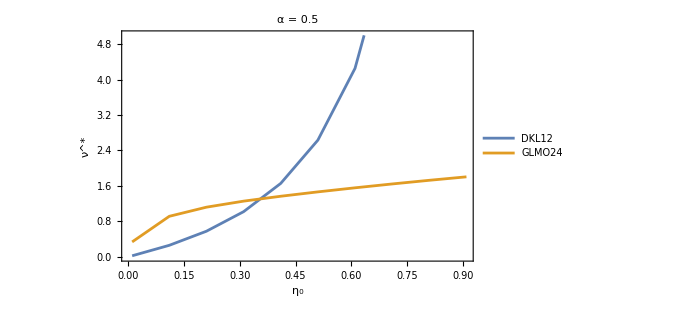

```mathematica
(* first fix α = 0.5 and make η vary*)
etavals = Range[0.01,1,0.1];(*0.05*)
(*NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->0.5,η->0.1},ν>0.5},ν]*)
GLMOetaresults = Table[ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->0.5,η->etavals[[i]]},ν>0.05},ν][[2]],{i,1,Length[etavals]}]
DKLetaresultsnum = Table[ν/.NMinimize[{Abs[cgeq2[ν]-DKL[η,ν, 1]]/.{η->etavals[[i]]},ν>0.05},ν][[2]],{i,1,Length[etavals]}]
DKLetaresults = Table[(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η)/.{η->etavals[[i]]},{i,1,Length[etavals]}]
(*Table[NMinimize[{Abs[cgeq2[ν]-DKL[η,ν, 1]]/.{η->etavals[[i]]},ν>0.1},ν,PrecisionGoal->50],{i,1,Length[etavals]}]*)
p = ListLinePlot[{Transpose[{etavals,DKLetaresults}],Transpose[{etavals,GLMOetaresults}]},PlotLegends->{"DKL12","GLMO24"},PlotStyle->{Directive[ColorData[1],AbsoluteThickness[2]],Directive[ColorData[2],AbsoluteThickness[2]]},PlotRange->{0,5},Frame->True,LabelStyle->20,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{"η_0", Rotate["ν^*",270 Degree]},ImageSize->500,FrameTicksStyle->18,LabelStyle->{Directive[20,Black]},PlotLabel-> "α = 0.5",BaseStyle->texStyle](*Red,Blue*)
(*Export["/Users/mgarnier/Documents/GitHub/MG-INRIA/Code/WCP-SDQC/MAthematica/NBFigs/fig_eta.pdf",p];*)
```

{0.01,0.11,0.21,0.31,0.41,0.51,0.61,0.71,0.81,0.91}

{5.11761,2.66481,2.01601,1.61504,1.31851,1.08,0.877244,0.696001,0.523321,0.338126}

{0.538553,0.538553,0.538553,0.538553,0.538553,0.538553,0.538553,0.538553,0.538553,0.538553}

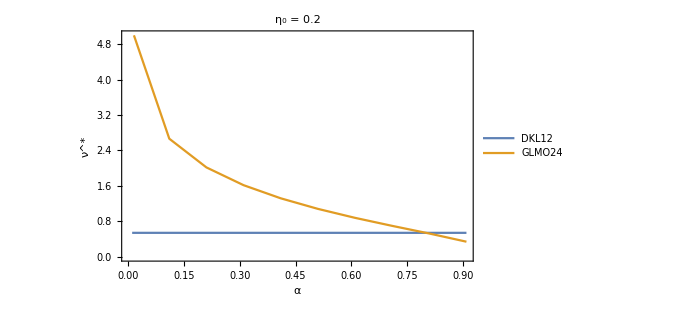

```mathematica
(* fix η = 0.2 and make α vary*)
alphavals = Range[0.01,1,0.1] (*0.05*)
(*NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->0.5,η->0.1},ν>0.5},ν]*)
GLMOalpharesults = Table[ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->alphavals[[i]],η->0.2},ν>0.05},ν][[2]],{i,1,Length[alphavals]}]
(*DKLetaresultsnum = Table[ν/.NMinimize[{Abs[cgeq2[ν]-DKL[η,ν, 1]]/.{η->etavals[[i]]},ν>45},ν,PrecisionGoal->50][[2]],{i,1,Length[etavals]}]*)
DKLalpharesults = Table[(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η)/.{η->0.2},{i,1,Length[alphavals]}]
(*Table[NMinimize[{Abs[cgeq2[ν]-DKL[η,ν, 1]]/.{η->etavals[[i]]},ν>0.1},ν,PrecisionGoal->50],{i,1,Length[etavals]}]*)
pp = ListLinePlot[{Transpose[{alphavals,DKLalpharesults}],Transpose[{alphavals,GLMOalpharesults}]},PlotLegends->{"DKL12","GLMO24"},PlotStyle->{ColorData[1],ColorData[2]},PlotRange->{0,5},Frame->True,LabelStyle->20,FrameStyle->Directive[AbsoluteThickness[2],Black],FrameLabel->{"α", Rotate["ν^*",270Degree]},ImageSize->500,FrameTicksStyle->18,LabelStyle->20,PlotLabel-> "η_0 = 0.2",BaseStyle->texStyle]
(*Export["/Users/mgarnier/Documents/GitHub/MG-INRIA/Code/WCP-SDQC/MAthematica/NBFigs/fig_alpha.pdf",pp];*)
```

### Density plot (function)

```mathematica
(* density plot: conditional function *)

(*condfunc [α_,η_]:= If[(ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])],ν>0.5},ν][[2]] )>(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η),1, If[(ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])],ν>0.5},ν][[2]]) <(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η),-1,0]];*)

lineStyle={Thick,White,Dashed};
lineStyle2={Thick,Black,Dashed};
line1=Line[{{0,0.2},{1,0.2}}];
line2=Line[{{0.5,0},{0.5,1}}];
condfunc [α_,η_]:= If[(ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])],ν>0.05},ν][[2]] )>(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η),1, -1];
condfunc[0.9,0.2]
(*or precompute values and test based on data*)
```

-1

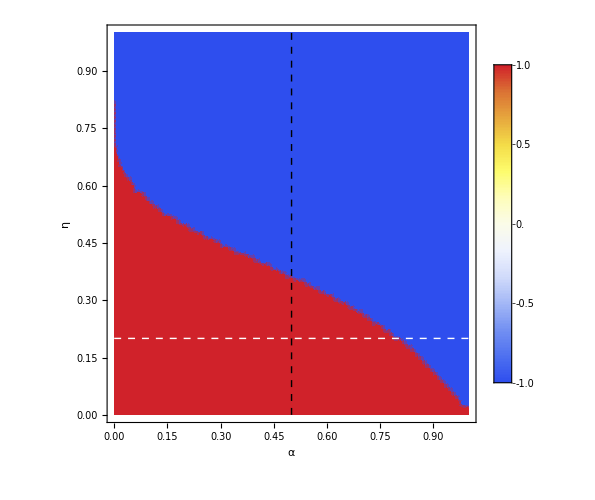

```mathematica
pplot=DensityPlot[condfunc [ α,η],{α,0,1},{η,0,1},PlotPoints->50,Frame->True,FrameLabel->{"α",Rotate["η_0",270 Degree]},BaseStyle->texStyle,FrameStyle->Directive[AbsoluteThickness[2],Black],ImageSize->500,FrameTicksStyle->18,LabelStyle->20,Epilog->{Directive[lineStyle],line1,Directive[lineStyle2],line2},ColorFunction->"TemperatureMap",PlotLegends->Automatic]
Export["/Users/mgarnier/Documents/GitHub/MG-INRIA/Code/WCP-SDQC/MAthematica/NBFigs/density_plot.pdf",pplot];
```

### Density plot (table)

```mathematica
alphavals = Range[0.05,0.99,0.05];
etavals = Range[0.05,0.99,0.05];
(*GLMOResutlsTable = Table[ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->alphavals[[i]],η->etavals[[k]]},ν>0.5},ν][[2]],{i,0,Length[alphavals]} ,{k,0,Length[etavals]}]*)
GLMOResultsTable=Table[ν/.NMinimize[{Abs[(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])-GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])]/.{α->alphavals[[i]],η->alphavals[[k]]},ν>0.05},ν][[2]],{i,1,Length[alphavals]},{k,1,Length[alphavals]}]
DKLResultsTable=Table[(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η)/.{α->alphavals[[i]],η->alphavals[[k]]},{i,1,Length[alphavals]},{k,1,Length[alphavals]}]
func[i_,j_]:=If[GLMOResultsTable[[i]][[j]]-DKLResultsTable[[i]][[j]] >0,1,-1]
ResultsTable = Table[func[m,n],{m,1,Length[alphavals]},{n,1,Length[alphavals]}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NMinimize::cvmit will be suppressed during this calculation.

{{3.15036,3.26952,3.36464,3.45437,3.54219,3.62898,3.7149,3.79981,3.88346,3.96554,4.04575,4.12382,4.19949,4.2726,4.34299,4.41058,4.47533,4.53726,4.5964},{2.41934,2.57638,2.67528,2.75984,2.83909,2.91595,2.9915,3.06613,3.13991,3.21274,3.28445,3.35483,3.42366,3.49071,3.5558,3.61877,3.6795,3.7379,3.79391},{1.96619,2.16054,2.26929,2.35507,2.43187,2.50445,2.57479,2.64377,2.71175,2.77884,2.84501,2.91012,2.97403,3.03654,3.09748,3.15667,3.21397,3.26927,3.32246},{1.63741,1.8581,1.97673,2.0655,2.14199,2.21251,2.27977,2.34507,2.40907,2.47204,2.53407,2.59514,2.65514,2.71395,2.7714,2.82734,2.88163,2.93414,2.98476},{1.38493,1.61968,1.7461,1.83794,1.9149,1.98433,2.04955,2.11223,2.17323,2.23298,2.2917,2.34944,2.40617,2.46179,2.51619,2.56924,2.6208,2.67075,2.71898},{1.18504,1.42365,1.55502,1.64928,1.72678,1.79552,1.85925,1.91987,1.97844,2.03554,2.09145,2.14633,2.20018,2.25298,2.30463,2.35503,2.40406,2.45162,2.49758},{1.02318,1.25825,1.39173,1.48738,1.56515,1.63328,1.69573,1.7546,1.81109,1.86586,1.91931,1.97162,2.02288,2.07308,2.12219,2.17011,2.21676,2.26204,2.30584},{0.88958,1.11614,1.24918,1.34506,1.42264,1.49001,1.55122,1.60848,1.66307,1.71572,1.7669,1.81685,1.86569,1.91347,1.96017,2.00573,2.0501,2.09318,2.13489},{0.777333,0.992257,1.12269,1.21768,1.29447,1.36082,1.42071,1.47637,1.52912,1.57976,1.62879,1.67649,1.72303,1.76848,1.81287,1.85616,1.8983,1.93923,1.97889},{0.681459,0.882871,1.00897,1.10196,1.17735,1.24232,1.30071,1.35469,1.40559,1.45425,1.50116,1.54668,1.59098,1.63417,1.67629,1.71734,1.75729,1.7961,1.83371},{0.598266,0.785111,0.905479,0.995495,1.06882,1.13202,1.18864,1.2408,1.28977,1.33639,1.38119,1.42452,1.46659,1.50752,1.54739,1.58621,1.62397,1.66065,1.69621},{0.524949,0.696668,0.810211,0.896344,0.966963,1.02792,1.08248,1.13258,1.17948,1.22397,1.26659,1.30768,1.34748,1.38613,1.42372,1.46029,1.49583,1.53035,1.56382},{0.5,0.615619,0.721438,0.802859,0.870114,0.928338,0.980451,1.02824,1.07285,1.11505,1.15536,1.19412,1.23157,1.26787,1.30311,1.33735,1.37062,1.40292,1.43424},{0.5,0.54027,0.637588,0.71351,0.77673,0.831678,0.880915,0.926035,0.968084,1.00777,1.04557,1.08184,1.11681,1.15063,1.18341,1.21523,1.24612,1.27609,1.30516},{0.5,0.5,0.557095,0.626724,0.685194,0.736254,0.7821,0.824122,0.863244,0.900103,0.935144,0.968685,1.00095,1.03211,1.06226,1.09149,1.11984,1.14734,1.17401},{0.5,0.5,0.5,0.540654,0.59356,0.640007,0.681828,0.720198,0.75591,0.789516,0.821414,0.85189,0.881153,0.909358,0.936614,0.963002,0.988578,1.01338,1.03743},{0.5,0.5,0.5,0.5,0.5,0.539952,0.576909,0.610874,0.642499,0.672243,0.700443,0.727347,0.753139,0.777959,0.801911,0.825075,0.847508,0.869252,0.89034},{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.516485,0.541403,0.565015,0.58752,0.609069,0.629779,0.649742,0.669029,0.687695,0.705784,0.723328},{0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.51244}}

{{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783},{0.107078,0.230163,0.372573,0.538553,0.733601,0.964959,1.24233,1.57901,1.99358,2.51286,3.17673,4.04697,5.22407,6.88189,9.34665,13.302,20.4328,36.1495,90.2783}}

{{1,1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1},{1,1,1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}}

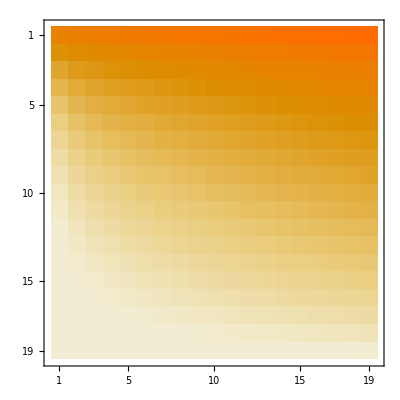

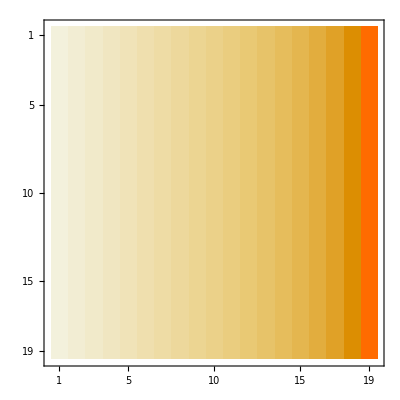

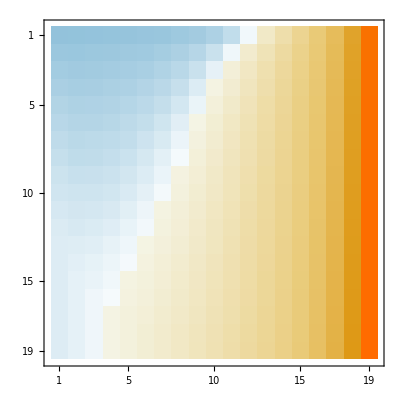

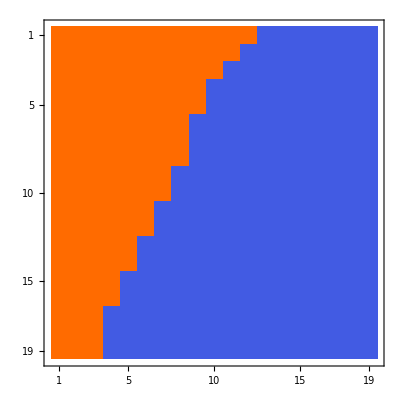

```mathematica
MatrixPlot[GLMOResultsTable]
MatrixPlot[DKLResultsTable]
MatrixPlot[DKLResultsTable-GLMOResultsTable]
MatrixPlot[ResultsTable]
```

```mathematica
SolDKL[η_]:=(1-η+ProductLog[ⅇ^(-1+η) (-1+η)])/(-1+η);
ⅇ^(-1+η) (-1+η)/.{η->0.2} 
ProductLog[ⅇ^(-1+η) (-1+η)]/.{η->0.2} 
{(ProductLog[-1,ⅇ^(-1+η) (-1+η)]+1-η)/(η-1)}/.{η->0.1} 
{(ProductLog[0,ⅇ^(-1+η) (-1+η)]+1-η)/(η-1)}/.{η->0.1} 
(1-η+ProductLog[ⅇ^(-1+η) (-1+η)])/.{η->0.3} 
(-0.9+0.8)/-0.8
NMinimize[{Abs[cgeq2[ν]-DKL[0.1,ν, 1]],ν>0.05},ν]
(2η)/(1-η)/.{η->0.4}
SolDKL[0.2]
```

-0.359463

-0.8

{0.230163}

{-1.23358×10^-16}

0.

0.125

{3.80454×10^-12,{ν→0.230163}}

1.33333

0.

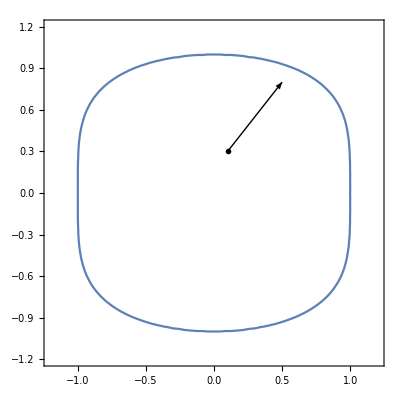

```mathematica
ContourPlot[x^2+y^4==1,{x,-1.2,1.2},{y,-1.2,1.2},BaseStyle->texStyle,Epilog->{Arrow[{{0.1,0.3},{0.5,0.80}}],Inset[MaTeX["x^2+y^4=1",Magnification->2],{0.1,0.3},Scaled[{0.5,1}]]}]
```

77

0

66

-88

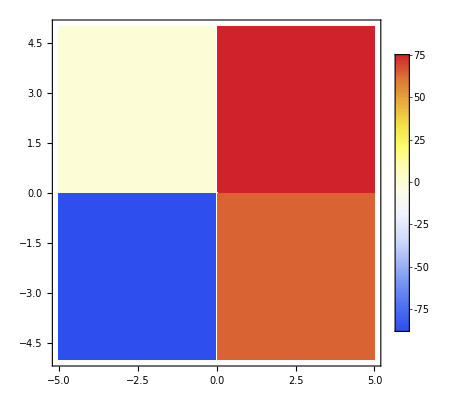

```mathematica
f[x_,y_]:=If[x>=0&&y>=0,77,If[x>=0&&y<0,66,If[x<0&&y>=0,0,If[x<0&&y<0,-88]]]]
f[1,2]
f[-1,2]
f[1,-2]
f[-1,-2]
DensityPlot[f[x,y],{x,-5,5},{y,-5,5}, PlotPoints->50,PlotLegends->Automatic,ColorFunction->"TemperatureMap"]
(*RegionPlot[{(c[ν]cgeq3[α ν])/(b[α ν]c[ν]-b[ν]c[α ν])<GLMO[η,α ν,ν, 2]/(b[α ν]c[ν]-b[ν]c[α ν])}/.{η->0.2,α->0.5},{ν,0,2},{y,0,0.5},PlotStyle->{LightRed,Opacity[.7]}]*)
```

```mathematica
lineStyle={Thick,White,Dashed};
lineStyle2={Thick,Black,Dashed};
line1=Line[{{-5,1},{5,1}}];
line2=Line[{{1,-5},{1,5}}];
```

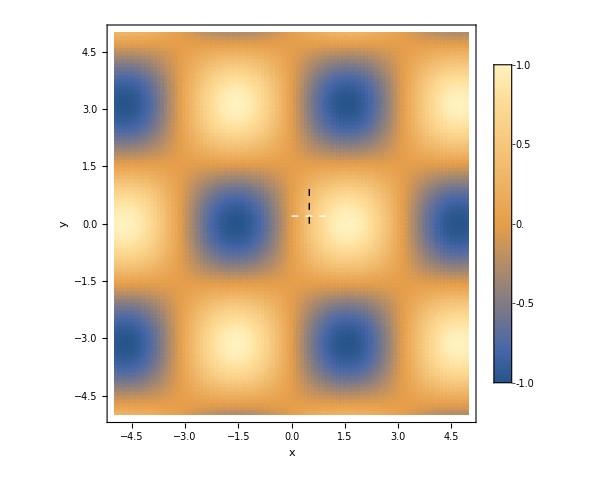

```mathematica
DensityPlot[Sin[x ]Cos[y],{x,-5,5},{y,-5,5}, PlotPoints->100,Frame->True,FrameLabel->{"x",Rotate["y",270]},BaseStyle->texStyle,FrameStyle->Directive[AbsoluteThickness[2],Black],ImageSize->500,FrameTicksStyle->18,LabelStyle->20,Epilog->{Directive[lineStyle],line1,Directive[lineStyle2],line2},PlotLegends->Automatic]
```

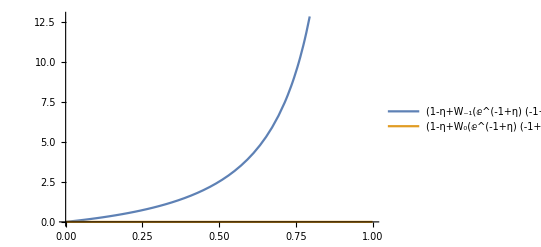

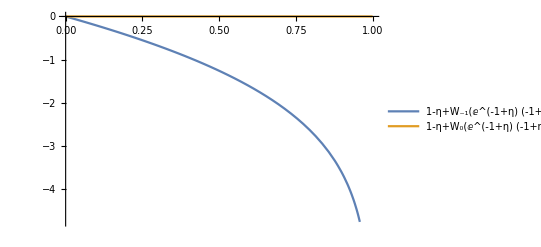

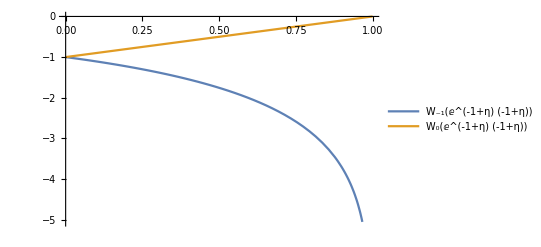

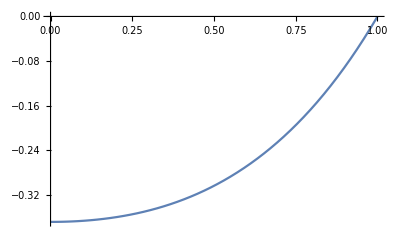

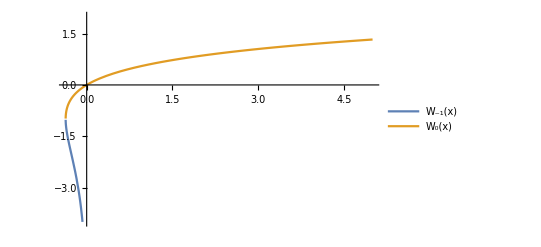

```mathematica
Plot[{(1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)])/(-1+η),(1-η+ProductLog[0,ⅇ^(-1+η) (-1+η)])/(-1+η)},{η,0,1},PlotLegends->"Expressions"]
Plot[{1-η+ProductLog[-1,ⅇ^(-1+η) (-1+η)],1-η+ProductLog[0,ⅇ^(-1+η) (-1+η)]},{η,0,1},PlotLegends->"Expressions"]
Plot[{ProductLog[-1,ⅇ^(-1+η) (-1+η)],ProductLog[0,ⅇ^(-1+η) (-1+η)]},{η,0,1},PlotLegends->"Expressions"]
Plot[ⅇ^(-1+η) (-1+η),{η,0,1},PlotLegends->Automatic]
Plot[{ProductLog[-1,x],ProductLog[0,x]},{x,-1,5},PlotLegends->"Expressions",PlotRange->{-4,2}]
```

```mathematica
-1/ⅇ//N
```

-0.367879